```mathematica
SetDirectory[NotebookDirectory[]]
pblue=Lighter[Blue];
pyellow=Lighter[Yellow];
pred=Lighter[Red];
pgreen=Lighter[Green];
cf=Piecewise[{{Blend[{pred,pblue},(#+Pi)/(Pi/2)],#≤-Pi/2},{Blend[{pblue,pgreen},(#+Pi/2)/(Pi/2)],#≤0},{Blend[{pgreen,pyellow},(#)/(Pi/2)],#≤Pi/2},{Blend[{pyellow,pred},(#-Pi/2)/(Pi/2)],#≤Pi}}]&;
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]]
phase[l:{_?NumericQ..}]:=Module[{args=Arg[l]},args+Prepend[2Pi Accumulate@-IntegerPart@Differences[args/Pi],0]]
nmax=10;
getphase[sig_]:=Module[{asig,plst,S1,slst1,f1},
asig=Fourier[ReplacePart[InverseFourier[sig-Mean[sig]],Join[{{1}},{#}&/@(Floor[Length[sig]/2]+Range[Floor[Length[sig]/2]])]->0]];
plst=phase[asig];
S1[n_]:=Sum[Exp[-I*n*plst[[i]]], {i,1,Length[plst]}]/Length[plst];
slst1=Table[S1[n]/(I*n),{n,1,nmax}];
f1[θ_]:=θ+Evaluate[Sum[2*Re[slst1][[n]]*(Cos[n*θ]-1)-2*Im[slst1][[n]]*Sin[n*θ],{n,1,nmax}]];
f1/@plst]
```

/home/zack/Desktop/snakingoscillators

### Janus oscillators

#### Single trajectory runs

-Graphics-

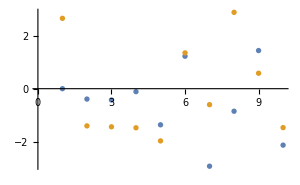
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
filebase="data/chimeras/2";
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
{seed,order,period,norm}=Import[filebase<>"out.dat"][[-1]];
M=10;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
orders=BinaryReadList[filebase<>"order.npy","Real64"][[17;;-1]];
rasterizeBackground[ListPlot[orders,ImageSize->300]]
phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
dphases=(Mod[#-#[[1]]+Pi,2*Pi]-Pi&/@phases);

If[period>0,
nperiod=Round[period/0.1];
Grid[{{rasterizeBackground[ListDensityPlot[dphases[[1;;nperiod,1;;M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[dphases[[1;;nperiod,M+1;;2*M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]]
If[Length[periods]>0,{period,Mean[orders[[-period;;-1]]],Norm[Differences[dphases[[-period+1;;-1]]],2]}]
```

```mathematica
Mean[Table[Abs[Sum[1/(2*M)*(Exp[I*theta[[n,i]]]+Exp[I*phi[[n,i]]]),{i,1,M}]]^2,{n,1,nperiod}]]^0.5
Mean[Table[Abs[Sum[1/(2*M)*(Exp[I*(theta[[n,i]]+2*Pi/M*(i-1))]+Exp[I*(phi[[n,i]]+2*Pi/M*(i-1))]),{i,1,M}]]^2,{n,1,nperiod}]]^0.5
Mean[Table[Abs[Sum[1/(2*M)*(Exp[I*(theta[[n,i]]-2*Pi/M*(i-1))]+Exp[I*(phi[[n,i]]-2*Pi/M*(i-1))]),{i,1,M}]]^2,{n,1,nperiod}]]^0.5
```

0.309461

0.276882

0.219461

#### AUTO periodic ics

```mathematica
vals={#[[1]],#[[2]],#[[3]]/300,#[[4]]}&/@SortBy[Import["random.dat"],Norm[#[[2;;4]]]&];
dorder=0.01;
dperiod=0.01;
dnorm=0.01;
{bins,array}=HistogramList[vals[[All,2;;4]],{{dorder*(Range[1/dorder]-1)},{0.1+dperiod*(Range[3/dperiod]-1)},{dnorm*(Range[2/dnorm]-1)}}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[2]]>=bins[[1,i]]&&u[[2]]<=bins[[1,i+1]]&&u[[3]]>=bins[[2,j]]&&u[[3]]<=bins[[2,j+1]]&&u[[4]]>=bins[[3,k]]&&u[[4]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
Length[uniq]
SortBy[{#[[1]],#[[2]],#[[3]]*300,#[[4]]}&/@uniq,{#[[2]],#[[3]],#[[4]]}&]

If[!DirectoryQ["data/chimeras"],CreateDirectory["data/chimeras"]]
seeds=uniq[[All,1]];
Do[CopyFile["data/random/"<>ToString[seeds[[i]]]<>"fs.npy","data/chimeras/"<>ToString[i]<>"ic.npy",OverwriteTarget->True], {i,1,Length[seeds]}]
Last/@ArrayRules[array][[1;;-2]]
```

10

{{822,7.86954×10^-16,43.7141,0.237467},{199,0.309889,93.0462,1.62203},{88,0.444722,92.9085,1.10769},{441,0.505823,93.3858,0.480243},{28,0.505863,93.3858,0.479485},{326,0.53729,90.2009,0.273056},{417,0.540555,88.9955,0.275255},{567,0.57116,93.9305,0.164956},{70,0.579997,92.9358,0.597037},{361,0.717616,93.9533,0.0818283}}

{1,1,18,2,1,2,3,63,1,211}

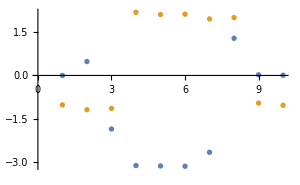
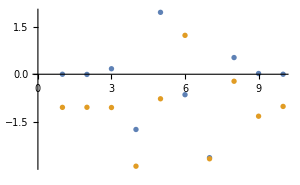
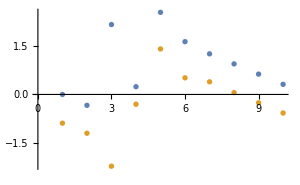
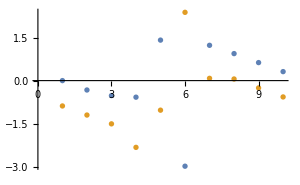
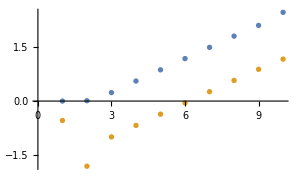
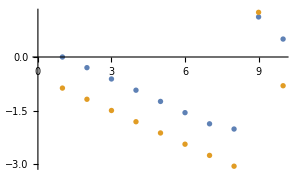
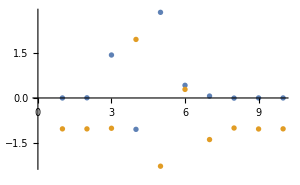
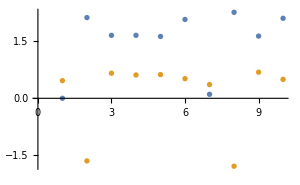
1 | 2.44131×10^-16 | 43.7142 | 0.238113 | 2.4261 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
2 | 0.309914 | 93.0462 | 1.62156 | 24.8733 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
3 | 0.444715 | 92.9096 | 1.10854 | 3.89638 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
4 | 0.505831 | 93.3865 | 0.480094 | 4.12425 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
5 | 0.505873 | 93.3865 | 0.479502 | 3.98015 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
6 | 0.53729 | 90.2019 | 0.27434 | 0.218262 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
7 | 0.540619 | 88.9964 | 0.275104 | 0.689971 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
8 | 0.579997 | 92.9365 | 0.597456 | 12.4475 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
9 | 0.571151 | 93.9308 | 0.165257 | 10.318 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
10 | 0.717596 | 93.9538 | 0.0822271 | 10.9378 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Monitor[p=Grid[DeleteCases[Table[filebase="data/chimeras/"<>ToString[j];
{seed,order,period,norm}=Import[filebase<>"out.dat"][[-1]];
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=10;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
phases2=Transpose[Catenate[{-Reverse[Transpose[phi]],-Reverse[Transpose[theta]]}]];
dphases=(Mod[#-#[[1]]+Pi,2*Pi]-Pi&/@phases);
dphases2=(#-#[[1]]&/@phases2);
norms=Norm[Mod[#-dphases[[-1]]+Pi,2*Pi]-Pi]&/@dphases;
mins=First/@Position[Differences[Sign[Differences[norms]]],u_/;u>0];
periods=Differences[Cases[mins,u_/;norms[[u]]<1]];
test=Norm[Mod[dphases[[-Round[period/0.1];;-1]]-dphases[[-10*Round[period/0.1];;-9*Round[period/0.1]-1]]+Pi,2*Pi]-Pi];
If[period>0,
{Grid[{{j,order,period,norm,test,rasterizeBackground[ListDensityPlot[dphases[[1;;Round[period/0.1];;10,1;;M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[dphases[[1;;Round[period/0.1];;10,M+1;;2*M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases2[[All,2]]],Cos[dphases2[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]}],{j,1,Length[uniq]}],Null]],j]
```

#### AUTO steady ics

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{η→-2.36793},{η→-1.49156}}

{1:0.809017,2:0.309017,3:-0.309017,4:-0.809017,5:-1.0,6:-0.809017,7:-0.309017,8:0.309017,9:0.809017,10:0.587785,11:0.951057,12:0.951057,13:0.587785,14:0.0,15:-0.587785,16:-0.951057,17:-0.951057,18:-0.587785,19:-0.715353,20:-0.16801,21:0.443507,22:0.88562,23:0.989455,24:0.715353,25:0.16801,26:-0.443507,27:-0.88562,28:-0.989455,29:-0.698763,30:-0.985785,31:-0.896271,32:-0.464411,33:0.144838,34:0.698763,35:0.985785,36:0.896271,37:0.464411,38:-0.144838}

{-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2}

{0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2}

2.48253×10^-17

1.24127×10^-17

0.377258

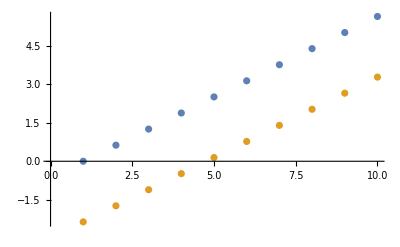

{1:0.809017,2:0.309017,3:-0.309017,4:-0.809017,5:-1.0,6:-0.809017,7:-0.309017,8:0.309017,9:0.809017,10:0.587785,11:0.951057,12:0.951057,13:0.587785,14:0.0,15:-0.587785,16:-0.951057,17:-0.951057,18:-0.587785,19:0.0791545,20:0.649978,21:0.972533,22:0.923612,23:0.521904,24:-0.0791545,25:-0.649978,26:-0.972533,27:-0.923612,28:-0.521904,29:-0.996862,30:-0.759953,31:-0.232767,32:0.383328,33:0.853004,34:0.996862,35:0.759953,36:0.232767,37:-0.383328,38:-0.853004}

{-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2}

{0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2}

2.22045×10^-17

3.14018×10^-17

0.734559

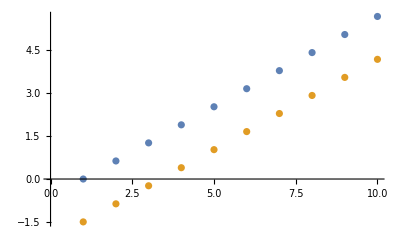

```mathematica
sols=Solve[0==1+2*0.25*Sin[η]+2*0.33*Sin[η+2*Pi/M],η]
thetas=Table[2*Pi/M*i,{i,1,M-1}];
phis=Table[η+2*Pi/M*i,{i,0,M-1}]/.sols[[1]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]

theta=N[Join[{0},thetas]];
Table[ω/2+β*Sin[phis[[i]]-theta[[i]]]+σ*Sin[phis[[Mod[i+1-1,M]+1]]-theta[[i]]],{i,1,M}]
Table[-ω/2+β*Sin[theta[[i]]-phis[[i]]]+σ*Sin[theta[[Mod[i-1-1,M]+1]]-phis[[i]]],{i,1,M}]
Abs[Total[Exp[I*theta]+Exp[I*phis]]/(2*M)]
Abs[Total[Exp[I*(theta+2*Pi*Range[M]/M)]+Exp[I*(phis+2*Pi*Range[M]/M)]]/(2*M)]
Abs[Total[Exp[I*(theta-2*Pi*Range[M]/M)]+Exp[I*(phis-2*Pi*Range[M]/M)]]/(2*M)]
ListPlot[{theta,phis}]

thetas=Table[2*Pi/M*i,{i,1,M-1}];
phis=Table[η+2*Pi/M*i,{i,0,M-1}]/.sols[[2]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]

theta=N[Join[{0},thetas]];
Table[ω/2+β*Sin[phis[[i]]-theta[[i]]]+σ*Sin[phis[[Mod[i+1-1,M]+1]]-theta[[i]]],{i,1,M}]
Table[-ω/2+β*Sin[theta[[i]]-phis[[i]]]+σ*Sin[theta[[Mod[i-1-1,M]+1]]-phis[[i]]],{i,1,M}]
Abs[Total[Exp[I*theta]+Exp[I*phis]]/(2*M)]
Abs[Total[Exp[I*(theta+2*Pi*Range[M]/M)]+Exp[I*(phis+2*Pi*Range[M]/M)]]/(2*M)]
Abs[Total[Exp[I*(theta-2*Pi*Range[M]/M)]+Exp[I*(phis-2*Pi*Range[M]/M)]]/(2*M)]
ListPlot[{theta,phis}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{η→-1.65003},{η→-0.773667}}

{1:0.809017,2:0.309017,3:-0.309017,4:-0.809017,5:-1.0,6:-0.809017,7:-0.309017,8:0.309017,9:0.809017,10:-0.587785,11:-0.951057,12:-0.951057,13:-0.587785,14:0.0,15:0.587785,16:0.951057,17:0.951057,18:0.587785,19:-0.0791545,20:-0.649978,21:-0.972533,22:-0.923612,23:-0.521904,24:0.0791545,25:0.649978,26:0.972533,27:0.923612,28:0.521904,29:-0.996862,30:-0.759953,31:-0.232767,32:0.383328,33:0.853004,34:0.996862,35:0.759953,36:0.232767,37:-0.383328,38:-0.853004}

{-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2}

{0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2}

0.

0.678545

2.00148×10^-17

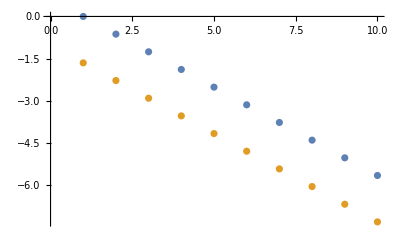

{1:0.809017,2:0.309017,3:-0.309017,4:-0.809017,5:-1.0,6:-0.809017,7:-0.309017,8:0.309017,9:0.809017,10:-0.587785,11:-0.951057,12:-0.951057,13:-0.587785,14:0.0,15:0.587785,16:0.951057,17:0.951057,18:0.587785,19:0.715353,20:0.16801,21:-0.443507,22:-0.88562,23:-0.989455,24:-0.715353,25:-0.16801,26:0.443507,27:0.88562,28:0.989455,29:-0.698763,30:-0.985785,31:-0.896271,32:-0.464411,33:0.144838,34:0.698763,35:0.985785,36:0.896271,37:0.464411,38:-0.144838}

{-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2}

{0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2}

4.44089×10^-17

0.926108

4.00297×10^-17

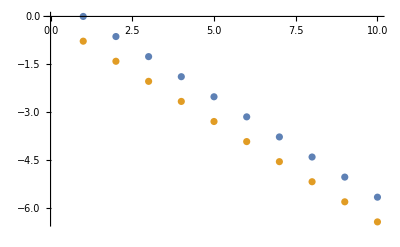

```mathematica
sols=Solve[0==1+2*0.25*Sin[η]+2*0.33*Sin[η-2*Pi/M],η]
thetas=Table[-2*Pi/M*i,{i,1,M-1}];
phis=Table[η-2*Pi/M*i,{i,0,M-1}]/.sols[[1]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]

theta=N[Join[{0},thetas]];
Table[ω/2+β*Sin[phis[[i]]-theta[[i]]]+σ*Sin[phis[[Mod[i+1-1,M]+1]]-theta[[i]]],{i,1,M}]
Table[-ω/2+β*Sin[theta[[i]]-phis[[i]]]+σ*Sin[theta[[Mod[i-1-1,M]+1]]-phis[[i]]],{i,1,M}]
Abs[Total[Exp[I*theta]+Exp[I*phis]]/(2*M)]
Abs[Total[Exp[I*(theta+2*Pi*Range[M]/M)]+Exp[I*(phis+2*Pi*Range[M]/M)]]/(2*M)]
Abs[Total[Exp[I*(theta-2*Pi*Range[M]/M)]+Exp[I*(phis-2*Pi*Range[M]/M)]]/(2*M)]
ListPlot[{theta,phis}]

thetas=Table[-2*Pi/M*i,{i,1,M-1}];
phis=Table[η-2*Pi/M*i,{i,0,M-1}]/.sols[[2]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]

theta=N[Join[{0},thetas]];
Table[ω/2+β*Sin[phis[[i]]-theta[[i]]]+σ*Sin[phis[[Mod[i+1-1,M]+1]]-theta[[i]]],{i,1,M}]
Table[-ω/2+β*Sin[theta[[i]]-phis[[i]]]+σ*Sin[theta[[Mod[i-1-1,M]+1]]-phis[[i]]],{i,1,M}]
Abs[Total[Exp[I*theta]+Exp[I*phis]]/(2*M)]
Abs[Total[Exp[I*(theta+2*Pi*Range[M]/M)]+Exp[I*(phis+2*Pi*Range[M]/M)]]/(2*M)]
Abs[Total[Exp[I*(theta-2*Pi*Range[M]/M)]+Exp[I*(phis-2*Pi*Range[M]/M)]]/(2*M)]
ListPlot[{theta,phis}]
```

```mathematica
η=0;
σ=0.33;
β=0.25;
ω=1;
θ1=0;
AbsoluteTiming[vals=Mod[{θ2,ϕ1,ϕ2},2*Pi]/.DeleteCases[Table[SeedRandom[seed];Quiet[Check[FindRoot[{0==ω/2+β*Sin[ϕ1]+σ*Sin[ϕ2+η],0==-ω/2+β*Sin[-ϕ1]+σ*Sin[θ2-ϕ1-η],0==ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η]},{{θ2,2*Pi*RandomReal[]},{ϕ1,2*Pi*RandomReal[]},{ϕ2,2*Pi*RandomReal[]}}],{}]],{seed,1,10000}],{}];]
dtheta=0.01;
{bins,array}=HistogramList[vals[[All,1;;3]],{{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)}}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[1]]>=bins[[1,i]]&&u[[1]]<=bins[[1,i+1]]&&u[[2]]>=bins[[2,j]]&&u[[2]]<=bins[[2,j+1]]&&u[[3]]>=bins[[3,k]]&&u[[3]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
{Length[uniq],Length[vals]}
SortBy[{#[[1]],#[[2]],#[[3]]}&/@uniq,{#[[1]],#[[2]],#[[3]]}&]
```

{8.65469,Null}

{162,9891}

{{2.50843×10^-16,4.18093,4.18093},{8.88178×10^-16,5.24385,5.24385},{0.00123161,4.18163,5.24438},{0.00296332,5.24553,4.18221},{0.012194,4.1879,5.24907},{0.0274871,5.25933,4.19294},{0.0363825,5.26427,4.19689},{0.0695026,4.22149,5.27279},{0.0971908,4.23821,5.28376},{0.109267,4.24561,5.28844},{0.11871,5.30845,4.23504},{0.123738,5.31105,4.23746},{0.146243,5.32258,4.24844},{0.164472,4.28022,5.30903},{0.181865,4.2914,5.31524},{0.202555,4.30488,5.32245},{0.210921,5.35451,4.28119},{0.2386,5.36761,4.29577},{0.251174,5.37345,4.3025},{0.258018,5.3766,4.3062},{0.272012,4.35157,5.34522},{0.286775,4.36179,5.34976},{0.294723,4.36734,5.35217},{0.313969,5.40151,4.33724},{0.348936,5.41632,4.35739},{0.354966,4.4104,5.36934},{0.36902,5.42455,4.36925},{0.379407,4.42842,5.37577},{0.397839,4.44222,5.3804},{0.407359,5.43968,4.39246},{0.413709,4.45425,5.38423},{0.46271,5.4601,4.42739},{0.465839,4.49483,5.39578},{0.466353,5.46138,4.42975},{0.475146,4.50225,5.39767},{0.475383,5.46453,4.43563},{0.537287,4.55326,5.4088},{0.542926,5.48643,4.48128},{0.562092,4.57438,5.41249},{0.571584,5.49479,4.50157},{0.595874,5.5014,4.51925},{0.603203,5.50331,4.52467},{0.608366,4.61506,5.41808},{0.61618,4.6221,5.41885},{0.653315,5.51516,4.56293},{0.663702,4.66613,5.42235},{0.664287,5.51746,4.5716},{0.711119,4.7123,5.42359},{0.722441,5.52765,4.61957},{0.731553,4.73298,5.42335},{0.752077,5.53139,4.64547},{0.779868,4.78403,5.42061},{0.788148,5.53439,4.67853},{0.789947,4.79511,5.41962},{0.798148,5.53489,4.68804},{0.806663,4.81383,5.41761},{0.851564,5.53465,4.74169},{0.852473,4.86775,5.4095},{0.864781,5.53372,4.75584},{0.887129,4.91158,5.40033},{0.904859,4.93524,5.39439},{0.910477,5.52715,4.8081},{0.927751,4.9673,5.38523},{0.929414,5.52256,4.83163},{0.947388,4.99642,5.37575},{0.964503,5.02328,5.366},{0.971165,5.50709,4.88885},{0.983718,5.50053,4.90797},{0.984633,5.0571,5.35231},{0.998236,5.49144,4.93157},{1.00197,5.08872,5.33802},{1.02396,5.13364,5.3151},{1.02946,5.14606,5.30818},{1.03024,5.463,4.99202},{1.03213,5.46079,4.99612},{1.03703,5.1642,5.2976},{1.04034,5.45018,5.01493},{1.04829,5.19434,5.27873},{1.05262,5.42999,5.0474},{1.06316,5.24486,5.24308},{1.06573,5.39668,5.09382},{1.07109,5.37261,5.12325},{1.07311,5.30471,5.19318},{1.07376,5.31378,5.18476},{1.07402,5.31894,5.17986},{5.20911,4.08237,4.26834},{5.20969,4.11513,4.23615},{5.21224,4.05129,4.30255},{5.21504,4.15648,4.20015},{5.21811,4.02587,4.33383},{5.22045,4.18167,4.18037},{5.23038,3.99515,4.37682},{5.23357,4.22658,4.14858},{5.23993,4.24447,4.13705},{5.24374,3.97335,4.41198},{5.25116,4.27272,4.12003},{5.25136,3.96362,4.42933},{5.25271,3.96205,4.43225},{5.2644,4.30233,4.10367},{5.29251,3.92838,4.50572},{5.297,4.36496,4.07364},{5.30148,3.92312,4.51995},{5.30727,4.38266,4.0662},{5.31436,3.91658,4.53937},{5.32859,4.41723,4.05295},{5.33473,4.42674,4.04959},{5.35856,4.46196,4.03819},{5.36561,3.8992,4.60801},{5.37284,3.8976,4.61683},{5.37899,4.49043,4.03015},{5.38425,4.49754,4.0283},{5.3899,3.89448,4.63701},{5.43322,4.56008,4.01473},{5.43432,3.88999,4.68593},{5.46348,4.596,4.00907},{5.46849,3.88942,4.72066},{5.48379,4.61914,4.00624},{5.49554,3.89042,4.74672},{5.52919,4.66848,4.0023},{5.53499,3.89382,4.78276},{5.555,4.69524,4.00135},{5.56225,3.89735,4.80649},{5.58182,4.72217,4.00124},{5.60953,3.90544,4.84568},{5.61626,4.75559,4.00227},{5.63251,3.91019,4.86392},{5.64374,4.78138,4.00395},{5.6579,3.91598,4.88351},{5.67883,4.81331,4.00711},{5.68664,3.9232,4.90504},{5.70529,4.8367,4.01019},{5.71003,3.92955,4.92207},{5.72628,3.9342,4.93367},{5.74714,4.87256,4.01617},{5.75645,3.94333,4.95471},{5.78989,4.9079,4.02359},{5.81303,4.92651,4.02811},{5.8154,3.96289,4.9941},{5.85469,4.95918,4.0371},{5.85804,3.97835,5.02128},{5.87491,3.98475,5.03175},{5.89255,3.99161,5.04254},{5.90127,4.99449,4.04837},{5.91506,5.00472,4.05194},{5.93703,4.00961,5.06901},{5.93738,5.02105,4.05793},{5.94873,4.01452,5.07581},{5.97423,5.04744,4.06839},{5.99395,5.06127,4.07427},{6.01889,4.04531,5.11517},{6.03223,4.05143,5.12239},{6.04275,5.09471,4.08963},{6.04582,4.05774,5.12967},{6.06579,5.11011,4.09727},{6.09647,4.082,5.15606},{6.10189,5.13374,4.10974},{6.11899,5.14474,4.11585},{6.13421,4.10081,5.175},{6.15448,4.11116,5.18491},{6.17538,5.18007,4.1369},{6.18357,5.18509,4.14007},{6.1845,4.12681,5.19928}}

```mathematica
Monitor[Do[{θ2,ϕ1,ϕ2}=uniq[[i]];
thetas=Riffle[Table[θ2+η*i,{i,1,M-1,2}],Table[0+η*i,{i,2,M-1,2}]];
phis=Riffle[Table[ϕ1+η*i,{i,0,M-1,2}],Table[ϕ2+η*i,{i,1,M-1,2}]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
lines=StringJoin[{Import["auto/clusters/c.cluster"],"\nU="<>ToString[Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]]}];
file=OpenWrite["auto/clusters/c.cluster"<>ToString[i]];
WriteLine[file,lines];
Close[file];,{i,1,Length[uniq]}],i]
```

```mathematica
η=2*Pi/M;
σ=0.33;
β=0.25;
ω=1;
θ1=0;
AbsoluteTiming[vals=Mod[{θ2,ϕ1,ϕ2},2*Pi]/.DeleteCases[Table[SeedRandom[seed];Quiet[Check[FindRoot[{0==ω/2+β*Sin[ϕ1]+σ*Sin[ϕ2+η],0==-ω/2+β*Sin[-ϕ1]+σ*Sin[θ2-ϕ1-η],0==ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η]},{{θ2,2*Pi*RandomReal[]},{ϕ1,2*Pi*RandomReal[]},{ϕ2,2*Pi*RandomReal[]}}],{}]],{seed,1,10000}],{}];]
dtheta=0.01;
{bins,array}=HistogramList[vals[[All,1;;3]],{{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)}}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[1]]>=bins[[1,i]]&&u[[1]]<=bins[[1,i+1]]&&u[[2]]>=bins[[2,j]]&&u[[2]]<=bins[[2,j+1]]&&u[[3]]>=bins[[3,k]]&&u[[3]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
{Length[uniq],Length[vals]}
uniq
```

{9.1742,Null}

{6,9331}

{{-1.35285×10^-16,3.91526,3.91526},{6.86275×10^-16,4.79163,4.79163},{0.370635,5.08302,4.71239},{0.445814,4.08407,4.52988},{5.83737,4.08407,3.63826},{5.91255,4.34175,4.71239}}

```mathematica
Monitor[Do[{θ2,ϕ1,ϕ2}=uniq[[i]];
thetas=Riffle[Table[θ2+η*i,{i,1,M-1,2}],Table[0+η*i,{i,2,M-1,2}]];
phis=Riffle[Table[ϕ1+η*i,{i,0,M-1,2}],Table[ϕ2+η*i,{i,1,M-1,2}]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
lines=StringJoin[{Import["auto/clusters1/c.cluster"],"\nU="<>ToString[Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]]}];
file=OpenWrite["auto/clusters1/c.cluster"<>ToString[i]];
WriteLine[file,lines];
Close[file];,{i,1,Length[uniq]}],i]
```

```mathematica
η=-2*Pi/M;
σ=0.33;
β=0.25;
ω=1;
θ1=0;
AbsoluteTiming[vals=Mod[{θ2,ϕ1,ϕ2},2*Pi]/.DeleteCases[Table[SeedRandom[seed];Quiet[Check[FindRoot[{0==ω/2+β*Sin[ϕ1]+σ*Sin[ϕ2+η],0==-ω/2+β*Sin[-ϕ1]+σ*Sin[θ2-ϕ1-η],0==ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η]},{{θ2,2*Pi*RandomReal[]},{ϕ1,2*Pi*RandomReal[]},{ϕ2,2*Pi*RandomReal[]}}],{}]],{seed,1,10000}],{}];]
dtheta=0.01;
{bins,array}=HistogramList[vals[[All,1;;3]],{{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)}}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[1]]>=bins[[1,i]]&&u[[1]]<=bins[[1,i+1]]&&u[[2]]>=bins[[2,j]]&&u[[2]]<=bins[[2,j+1]]&&u[[3]]>=bins[[3,k]]&&u[[3]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
{Length[uniq],Length[vals]}
uniq
```

{9.5684,Null}

{6,9366}

{{-2.29173×10^-16,4.63315,4.63315},{-6.8655×10^-17,5.50952,5.50952},{0.370635,5.08302,4.71239},{0.445814,5.34071,5.78652},{5.83737,5.34071,4.89489},{5.91255,4.34175,4.71239}}

```mathematica
Monitor[Do[{θ2,ϕ1,ϕ2}=uniq[[i]];
thetas=Riffle[Table[θ2+η*i,{i,1,M-1,2}],Table[0+η*i,{i,2,M-1,2}]];
phis=Riffle[Table[ϕ1+η*i,{i,0,M-1,2}],Table[ϕ2+η*i,{i,1,M-1,2}]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
lines=StringJoin[{Import["auto/clusters2/c.cluster"],"\nU="<>ToString[Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]]}];
file=OpenWrite["auto/clusters2/c.cluster"<>ToString[i]];
WriteLine[file,lines];
Close[file];,{i,1,Length[uniq]}],i]
```

#### Plots of sweeps

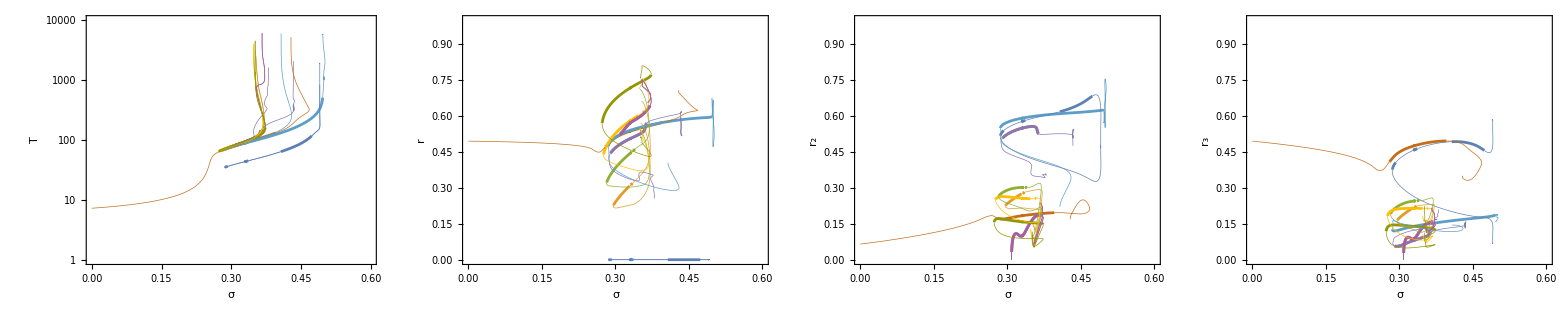

```mathematica
stable={};
unstable={};
M=10;
Do[
branch=Catenate[{Reverse[DeleteCases[Import["auto/chimeras/"<>ToString[i]<>"rv.dat"],{}]],DeleteCases[Import["auto/chimeras/"<>ToString[i]<>"fw.dat"],{}]}];
stables={};
unstables={};
part={};
stab=0;
Do[If[stab==0,If[branch[[i,7]]<4*M-2 , AppendTo[part,branch[[i]]];,stab=1;AppendTo[unstables,part];part={branch[[i]]};], If[branch[[i,7]]<4*M-2,stab=0;AppendTo[stables,part];part={branch[[i]]};,AppendTo[part,branch[[i]]];];];,{i,1,Length[branch]}];
If[stab==0,AppendTo[unstables,part],AppendTo[stables,part]];AppendTo[stable,stables];AppendTo[unstable,unstables];,{i,1,10}];

Grid[{{Show[Show[Table[ListLogPlot[stable[[i,All,All,{1,3}]],PlotRange->{{0,0.6},{1,10^4}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[i]]]],{i,1,10}]],Show[Table[ListLogPlot[unstable[[i,All,All,{1,3}]],PlotRange->{{0,0.6},{1,10^4}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5],ColorData[97,"ColorList"][[i]]]],{i,{1,2,3,5,6,7,8,9,10}}]]],Show[Show[Table[ListPlot[stable[[i,All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[i]]]],{i,1,10}]],Show[Table[ListPlot[unstable[[i,All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5],ColorData[97,"ColorList"][[i]]]],{i,{1,2,3,5,6,7,8,9,10}}]]],Show[Show[Table[ListPlot[stable[[i,All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[i]]]],{i,1,10}]],Show[Table[ListPlot[unstable[[i,All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5],ColorData[97,"ColorList"][[i]]]],{i,{1,2,3,5,6,7,8,9,10}}]]],Show[Show[Table[ListPlot[stable[[i,All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,3]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[i]]]],{i,1,10}]],Show[Table[ListPlot[unstable[[i,All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,3]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5],ColorData[97,"ColorList"][[i]]]],{i,{1,2,3,5,6,7,8,9,10}}]]]}}]
```

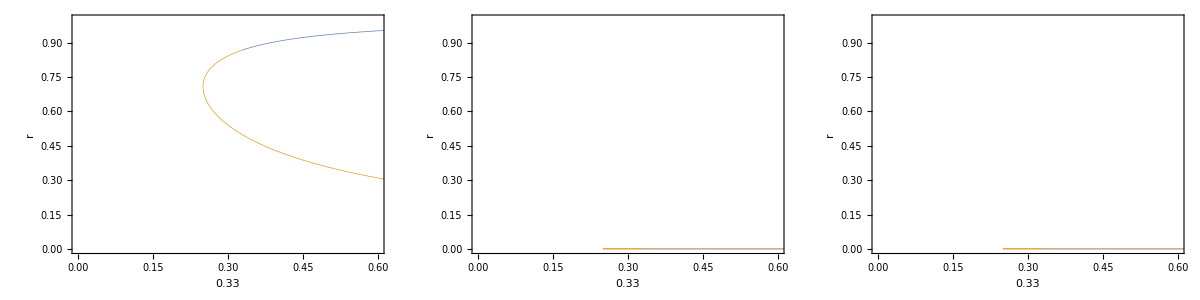

```mathematica
steady=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/steady/steady.dat"];
Grid[{{ListPlot[steady[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]],ListPlot[steady[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]],ListPlot[steady[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]}}]
```

```mathematica
twists1=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/twist1/twists.dat"];
Grid[{{rasterizeBackground[ListPlot[twists1[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[twists1[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[twists1[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
twists2=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/twist2/twists.dat"];
Grid[{{rasterizeBackground[ListPlot[twists2[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[twists2[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[twists2[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
clusters1=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/clusters1/clusters.dat"];
Grid[{{rasterizeBackground[ListPlot[clusters1[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[clusters1[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[clusters1[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
clusters2=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/clusters2/clusters.dat"];
Grid[{{rasterizeBackground[ListPlot[clusters2[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[clusters2[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[clusters2[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
all=Join[steady,twists1,twists2,clusters1,clusters2];
Grid[{{rasterizeBackground[ListPlot[all[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[all[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[all[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
AbsoluteTiming[Monitor[branches=Table[Import["auto/clusters/branches/"<>ToString[i]<>".dat"],{i,1,6099}];,i]]
```

{523.051,Null}

```mathematica
dist[branch1_,branch2_]:=Module[{min,max,c1,c2,f1,f2,x,range},
{min,max}={Max[{Min[branch1[[All,1]]],Min[branch2[[All,1]]]}],Min[{Max[branch1[[All,1]]],Max[branch2[[All,1]]]}]};
c1=Cases[DeleteDuplicatesBy[branch1,#[[1]]&],u_/;u[[1]]>=min&&u[[1]]<=max];
c2=Cases[DeleteDuplicatesBy[branch2,#[[1]]&],u_/;u[[1]]>=min&&u[[1]]<=max];
{min,max}={Max[{Min[c1[[All,1]]],Min[c2[[All,1]]]}],Min[{Max[c1[[All,1]]],Max[c2[[All,1]]]}]};
If[max>min&&Length[c1]>1&&Length[c2]>1,f1=Interpolation[c1[[All,{1,4}]],InterpolationOrder->1];
f2=Interpolation[c2[[All,{1,4}]],InterpolationOrder->1];
range=(max-min);
Sum[Abs[f1[x]-f2[x]],{x,min+range/100,max-range/100,range/100}]/range,Infinity]]
AbsoluteTiming[Monitor[distances=Flatten[Table[{i,j,dist[branches[[i]],branches[[j]]]},{i,1,1},{j,i+1,Length[branches]}],1];,{i,j}]]
Cases[distances,u_/;u[[1]]<1]
```

{39.8638,Null}

{}

```mathematica
AbsoluteTiming[rasterizeBackground[ListPlot[branches[[1;;4000,All,{1,4}]],PlotRange->{{0,1},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]]
```

{112.404,-Graphics-}

### pendula

#### Single trajectory runs

```mathematica
filebase="data/test1";
{M,t1,t0,dt,amp,omega}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
Grid[{{rasterizeBackground[ListPlot[Transpose[{dt*Range[Length[dat]],Norm[#[[1;;M]]]&/@dat}],Axes->False,Frame->True,FrameLabel->{t,norm},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1],Black],AspectRatio->1,ImageSize->300]],rasterizeBackground[ListDensityPlot[dat[[-Round[50/dt];;-1;;Round[1/dt],1;;M]],InterpolationOrder->0,Frame->True,FrameLabel->{i,t},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1],Black],AspectRatio->1,ImageSize->300,ColorFunctionScaling->False,ColorFunction->cf]]}}]

limit=Transpose[Catenate[{N[{2*Pi*dt*Range[0,1/dt]}],Transpose[Cos[dat[[Round[-1/dt]-1;;-1,1;;M;;2]]]],Transpose[Sin[dat[[Round[-1/dt]-1;;-1,1;;M;;2]]]],Transpose[dat[[Round[-1/dt]-1;;-1,M+1;;2*M;;2]]],Transpose[Cos[dat[[Round[-1/dt]-1;;-1,2;;M;;2]]]],Transpose[Sin[dat[[Round[-1/dt]-1;;-1,2;;M;;2]]]],Transpose[dat[[Round[-1/dt]-1;;-1,M+2;;2*M;;2]]],N[{Cos[2*Pi*dt*(Range[0,1/dt]-1)],Sin[2*Pi*dt*(Range[0,1/dt]-1)]}]}]];
Export["auto/pendula/flat.dat",limit];
```

{8,1000.,0.,0.05,0.04,3.4}

-Graphics- | -Graphics-

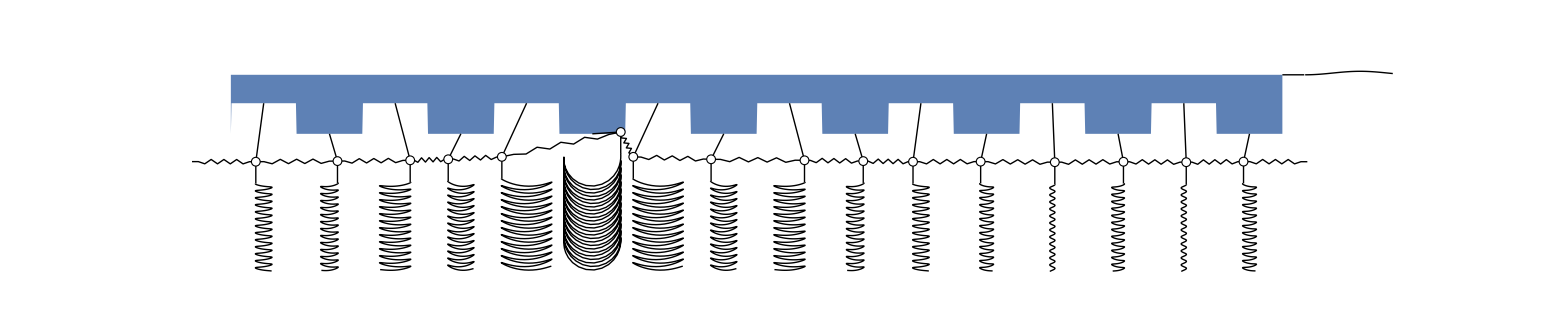

```mathematica
spring[p0_,p1_,divs_,height_]:=Module[{L,xhat,yhat},L=Norm[p1-p0]; xhat=(p1-p0)/L; yhat={xhat[[2]],-xhat[[1]]};Join[{p0,p0+L/divs*xhat},Table[p0+i*L/divs*xhat+height*yhat*(-1)^i,{i,2,divs-2}],{p1-L/divs*xhat,p1}]]

amax=amp;
ωd=1;
dx=1.5;
dn=500;
n1=Length[dat]-Round[2/dt];
n0=n1;
n=n1;
thetas=dat[[n,1;;M]];
thetas2=dat[[n-dn;;n,1;;M]];
lengths=Riffle[ConstantArray[0.35,M/2],ConstantArray[-0.35,M/2]];
f[x_]:=lengths[[1+Mod[Round[x/dx]-1,M]]];
z0={0,-amax*Cos[ωd*dt/ωd*(n-n0)]};
p0=Graphics[{ColorData[97,"ColorList"][[1]],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/100}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]],Black,Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]}}],{i,1,M}],
Table[Line[Table[{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas2[[dn+1-m,i]]],Cos[thetas2[[dn+1-m,i]]]}-{0,2/dn*m},{m,1,dn}]],{i,1,M}],

Line[{{dx*(M+1/2),z0[[2]]+2},{0.5+dx*(M+1/2),z0[[2]]+2}}],
Line[{0.5+dx*(M+1/2),2}+#&/@Transpose[{0.02*Range[101],Reverse[Table[-amax*Cos[ωd*dt/ωd*(m-n0)],{m,n-100,n,1}]]}]],

Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],White,Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}]},ImageSize->2000,PlotRange->{-2+dx*{1/2,M+3.5+1/2},{-3,3}}]
```

```mathematica
Max[Abs[Transpose[Sin[dat[[Round[-2/dt]-1;;-1,1;;M;;2]]]]]]
Max[Abs[Transpose[Sin[dat[[Round[-2/dt]-1;;-1,2;;M;;2]]]]]]
```

0.

0.

```mathematica
filebase="data/flat";
{M,t1,t0,dt,amp,omega}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
Grid[{{rasterizeBackground[ListPlot[Transpose[{dt*Range[Length[dat]],Norm[#[[1;;M]]]&/@dat}],Axes->False,Frame->True,FrameLabel->{t,norm},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1],Black],AspectRatio->1,ImageSize->300]],rasterizeBackground[ListDensityPlot[dat[[-Round[50/dt];;-1;;Round[1/dt],1;;M]],InterpolationOrder->0,Frame->True,FrameLabel->{i,t},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1],Black],AspectRatio->1,ImageSize->300,ColorFunctionScaling->False,ColorFunction->cf]]}}]

limit=Transpose[Catenate[{N[{2*Pi*dt*Range[0,1/dt]}],Transpose[Cos[dat[[Round[-1/dt]-1;;-1,1;;M;;2]]]],Transpose[Sin[dat[[Round[-1/dt]-1;;-1,1;;M;;2]]]],Transpose[dat[[Round[-1/dt]-1;;-1,M+1;;2*M;;2]]],Transpose[Cos[dat[[Round[-1/dt]-1;;-1,2;;M;;2]]]],Transpose[Sin[dat[[Round[-1/dt]-1;;-1,2;;M;;2]]]],Transpose[dat[[Round[-1/dt]-1;;-1,M+2;;2*M;;2]]],N[{Cos[2*Pi*dt*(Range[0,1/dt]-1)],Sin[2*Pi*dt*(Range[0,1/dt]-1)]}]}]];
Export["auto/pendula/small/flat.dat",limit];
```

{16,1000.,0.,0.05,0.01,3.5}

-Graphics- | -Graphics-

```mathematica
count=1;
Monitor[Grid[DeleteCases[Table[filebase="data/pendula"<>ToString[i];
{M,t1,t0,dt,amp,omega}=Import[filebase<>"out.dat"][[2]];
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
m1=Max[Abs[Transpose[Sin[dat[[Round[-2/dt]-1;;-1,1;;M;;2]]]]]];
m2=Max[Abs[Transpose[Sin[dat[[Round[-2/dt]-1;;-1,2;;M;;2]]]]]];
If[m1>0.01&&m2>0.01,
limit=Transpose[Catenate[{N[{2*Pi*dt*Range[0,2/dt]}],Transpose[Cos[dat[[Round[-2/dt]-1;;-1,1;;M;;2]]]],Transpose[Sin[dat[[Round[-2/dt]-1;;-1,1;;M;;2]]]],Transpose[dat[[Round[-2/dt]-1;;-1,M+1;;2*M;;2]]],Transpose[Cos[dat[[Round[-2/dt]-1;;-1,2;;M;;2]]]],Transpose[Sin[dat[[Round[-2/dt]-1;;-1,2;;M;;2]]]],Transpose[dat[[Round[-2/dt]-1;;-1,M+2;;2*M;;2]]],N[{Cos[2*Pi*dt*(Range[0,2/dt]-1)],Sin[2*Pi*dt*(Range[0,2/dt]-1)]}]}]];
Export["auto/pendula/limit"<>ToString[count]<>".dat",limit];count=count+1;{rasterizeBackground[ListPlot[Transpose[{dt*Range[Length[dat]],Norm[#[[1;;M]]]&/@dat}],Axes->False,Frame->True,FrameLabel->{t,norm},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1],Black],AspectRatio->1,ImageSize->300]],rasterizeBackground[ListDensityPlot[dat[[-Round[50/dt];;-1;;Round[1/dt],1;;M]],InterpolationOrder->0,Frame->True,FrameLabel->{i,t},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1],Black],AspectRatio->1,ImageSize->300,ColorFunctionScaling->False,ColorFunction->cf]]}],{i,1,10}],Null]],i]
```

-Graphics- | -Graphics-

#### Plots of sweeps

```mathematica
stable={};
unstable={};
branches={};
M=8;
Do[
branch=Import[file];
AppendTo[branches,branch];
stables={};
unstables={};
part={};
stab=0;
Do[If[stab==0,If[branch[[i,5]]<6*M+2 , AppendTo[part,branch[[i]]];,stab=1;AppendTo[unstables,part];part={branch[[i]]};], If[branch[[i,5]]<6*M+2,stab=0;AppendTo[stables,part];part={branch[[i]]};,AppendTo[part,branch[[i]]];];];,{i,1,Length[branch]}];
If[stab==0,AppendTo[unstables,part],AppendTo[stables,part]];AppendTo[stable,stables];AppendTo[unstable,unstables];,{file,FileNames["auto/pendula/branches/*.dat"]}];
unstable=DeleteCases[#,{}]&/@unstable;
stable=DeleteCases[#,{}]&/@stable;

istable=First/@Position[Length/@stable,u_/;u>0];
iunstable=First/@Position[Length/@unstable,u_/;u>0];
Grid[{{Show[Show[Table[ListPlot[stable[[i,All,All,{1,3}]],PlotRange->{{0,0.2},All},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,istable}]],Show[Table[ListPlot[unstable[[i,All,All,{1,3}]],PlotRange->{{0,0.2},All},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.1],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,iunstable}]],PlotRange->{{0,0.2},All}],Show[Show[Table[ListPlot[stable[[i,All,All,{1,7}]],PlotRange->{{0,0.2},All},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,istable}]],Show[Table[ListPlot[unstable[[i,All,All,{1,7}]],PlotRange->{{0,0.2},All},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.1],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,iunstable}]],PlotRange->{{0,0.2},All}],Show[Show[Table[ListPlot[stable[[i,All,All,{1,8}]],PlotRange->{{0,0.2},All},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,istable}]],Show[Table[ListPlot[unstable[[i,All,All,{1,8}]],PlotRange->{{0,0.2},All},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.1],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,iunstable}]],PlotRange->{{0,0.2},All}]}}]
```

-Graphics-

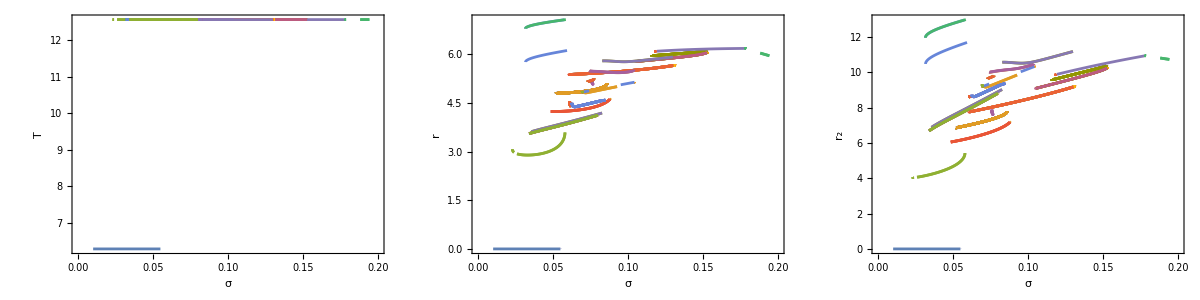

```mathematica
Grid[{{Show[Show[Table[ListPlot[stable[[i,All,All,{1,3}]],PlotRange->{{0,0.2},All},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,istable}]],PlotRange->{{0,0.2},All}],Show[Show[Table[ListPlot[stable[[i,All,All,{1,7}]],PlotRange->{{0,0.2},All},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,istable}]],PlotRange->{{0,0.2},All}],Show[Show[Table[ListPlot[stable[[i,All,All,{1,8}]],PlotRange->{{0,0.2},All},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,istable}]],PlotRange->{{0,0.2},All}]}}]
```

```mathematica
branches=Flatten[unstable,1];
Length[branches]

dist[branch1_,branch2_]:=Module[{min,max,c1,c2,f1,f2,x,range},
{min,max}={Max[{Min[branch1[[All,1]]],Min[branch2[[All,1]]]}],Min[{Max[branch1[[All,1]]],Max[branch2[[All,1]]]}]};
c1=Cases[DeleteDuplicatesBy[branch1,#[[1]]&],u_/;u[[1]]>=min&&u[[1]]<=max];
c2=Cases[DeleteDuplicatesBy[branch2,#[[1]]&],u_/;u[[1]]>=min&&u[[1]]<=max];
{min,max}={Max[{Min[c1[[All,1]]],Min[c2[[All,1]]]}],Min[{Max[c1[[All,1]]],Max[c2[[All,1]]]}]};
If[max>min&&Length[c1]>1&&Length[c2]>1,f1=Interpolation[c1[[All,{1,7}]],InterpolationOrder->1];
f2=Interpolation[c2[[All,{1,7}]],InterpolationOrder->1];
range=(max-min);
Sum[Abs[f1[x]-f2[x]],{x,min+range/100,max-range/100,range/100}]/range,Infinity]]
AbsoluteTiming[Monitor[distances=Flatten[Table[{i,j,dist[branches[[i]],branches[[j]]]},{i,1,Length[branches]},{j,i+1,Length[branches]}],1];,{i,j}]]
Cases[distances,u_/;u[[3]]<1]
```

360

{1752.92,Null}

{{9,155,0.0804596},{9,173,0.212176},{9,175,0.212177},{12,13,0.367533},{12,35,0.024508},{12,36,0.388644},{13,35,0.375902},{13,36,0.0793875},{15,16,0.346005},{15,37,0.370081},{15,38,0.387055},{16,37,0.0658712},{16,38,0.375609},{18,29,0.15654},{19,30,0.048663},{20,22,0.00116225},{20,24,0.00162025},{20,26,0.0011849},{20,28,1.39126×10^-6},{21,23,0.00471426},{21,25,0.00472945},{21,27,0.0000852404},{22,24,0.00118862},{22,26,2.85869×10^-6},{22,28,0.00116192},{23,25,0.0000682845},{23,27,0.0047188},{24,26,0.00118863},{24,28,0.0016209},{25,27,0.00473391},{26,28,0.00118596},{35,36,0.378054},{37,38,0.415386},{40,41,0.384696},{42,102,0.0104244},{43,45,0.00392745},{43,47,0.00389885},{43,49,0.0153827},{43,51,0.00411646},{43,53,0.0177622},{43,55,0.00410185},{43,57,0.00419497},{43,59,0.00419558},{43,61,0.00419487},{43,63,0.000768236},{43,65,0.00888274},{43,67,0.00870646},{43,69,0.00870288},{43,71,0.00870803},{43,73,0.019849},{43,76,0.01985},{43,78,0.0197821},{43,80,0.00862923},{43,82,0.00881535},{43,84,0.00882947},{44,46,9.36713×10^-8},{44,48,0.00243352},{44,50,0.000829366},{44,52,0.00257135},{44,54,0.00257138},{44,56,0.000829497},{44,58,0.000829545},{44,60,0.000829434},{44,62,0.0008295},{44,64,0.0103362},{44,66,0.00958771},{44,68,0.00958764},{44,70,0.00958781},{44,72,0.00958768},{44,74,0.00921621},{44,75,0.00921624},{44,77,0.00958767},{44,79,0.0111008},{44,81,0.00954726},{44,83,0.00954729},{44,85,0.00991594},{45,47,7.14746×10^-7},{45,49,0.0136244},{45,51,0.000620897},{45,53,0.0199459},{45,55,0.000619407},{45,57,0.000619199},{45,59,0.000619244},{45,61,0.000619183},{45,63,0.00398211},{45,65,0.00537979},{45,67,0.00537502},{45,69,0.00537201},{45,71,0.00537634},{45,73,0.0162256},{45,76,0.0162266},{45,78,0.0179362},{45,80,0.00528304},{45,82,0.00527584},{45,84,0.0052867},{46,48,0.00243702},{46,50,0.000829373},{46,52,0.00257454},{46,54,0.00257458},{46,56,0.000829504},{46,58,0.000829552},{46,60,0.00082944},{46,62,0.000829507},{46,64,0.0103362},{46,66,0.00958774},{46,68,0.00958767},{46,70,0.00958783},{46,72,0.00958771},{46,74,0.00921623},{46,75,0.00921626},{46,77,0.0095877},{46,79,0.0111012},{46,81,0.00954728},{46,83,0.00954732},{46,85,0.00991597},{47,49,0.0136238},{47,51,0.000620678},{47,53,0.0199297},{47,55,0.000619187},{47,57,0.000618979},{47,59,0.000619025},{47,61,0.000618964},{47,63,0.00390906},{47,65,0.00537186},{47,67,0.00537449},{47,69,0.00537888},{47,71,0.00537581},{47,73,0.0162251},{47,76,0.0162261},{47,78,0.0179356},{47,80,0.00527571},{47,82,0.00527532},{47,84,0.00528617},{48,50,0.00286986},{48,52,0.00252903},{48,54,0.00252891},{48,56,0.00286854},{48,58,0.00287169},{48,60,0.00287151},{48,62,0.00287167},{48,64,0.00932156},{48,66,0.00860072},{48,68,0.00859333},{48,70,0.00859313},{48,72,0.00859329},{48,74,0.00793759},{48,75,0.00793762},{48,77,0.00860084},{48,79,0.00949492},{48,81,0.00850896},{48,83,0.008509},{48,85,0.00904364},{49,51,0.0133334},{49,53,0.0285512},{49,55,0.0133783},{49,57,0.0133788},{49,59,0.0133782},{49,61,0.0133789},{49,63,0.0151663},{49,65,0.0121958},{49,67,0.0121927},{49,69,0.0121962},{49,71,0.012165},{49,73,0.00564073},{49,76,0.00564082},{49,78,0.00512878},{49,80,0.0121085},{49,82,0.0121087},{49,84,0.0120715},{50,52,0.00264701},{50,54,0.00264706},{50,56,2.50609×10^-6},{50,58,2.45088×10^-6},{50,60,2.33661×10^-6},{50,62,2.41493×10^-6},{50,64,0.0103947},{50,66,0.00964347},{50,68,0.0096434},{50,70,0.00964356},{50,72,0.00964344},{50,74,0.00921444},{50,75,0.00921446},{50,77,0.00964343},{50,79,0.0111448},{50,81,0.00961286},{50,83,0.0096129},{50,85,0.00997424},{51,53,0.0198664},{51,55,0.000015486},{51,57,0.0000160174},{51,59,0.0000153744},{51,61,0.0000161208},{51,63,0.00388978},{51,65,0.00526852},{51,67,0.00527115},{51,69,0.00526814},{51,71,0.00527247},{51,73,0.0180351},{51,76,0.0180359},{51,78,0.0177622},{51,80,0.00516782},{51,82,0.00516742},{51,84,0.00517763},{52,54,3.68262×10^-7},{52,56,0.00264929},{52,58,0.00264834},{52,60,0.00264832},{52,62,0.00264923},{52,64,0.00982929},{52,66,0.0092102},{52,68,0.00920514},{52,70,0.0092049},{52,72,0.00920508},{52,74,0.00939756},{52,75,0.00939753},{52,77,0.00921036},{52,79,0.0102765},{52,81,0.00906911},{52,83,0.00906914},{52,85,0.00954558},{53,55,0.0198535},{53,57,0.0198636},{53,59,0.0198641},{53,61,0.0198636},{53,63,0.0175755},{53,65,0.0197876},{53,67,0.019791},{53,69,0.0197878},{53,71,0.0197872},{53,73,0.0286137},{53,76,0.028614},{53,78,0.0294541},{53,80,0.0196079},{53,82,0.0196151},{53,84,0.0196211},{54,56,0.00264933},{54,58,0.00264838},{54,60,0.00264836},{54,62,0.00264841},{54,64,0.00982115},{54,66,0.00921022},{54,68,0.00920515},{54,70,0.00920491},{54,72,0.0092051},{54,74,0.00939757},{54,75,0.00939754},{54,77,0.00921037},{54,79,0.0102765},{54,81,0.00906914},{54,83,0.00906916},{54,85,0.00954562},{55,57,7.58079×10^-7},{55,59,1.05018×10^-6},{55,61,8.10719×10^-7},{55,63,0.00387506},{55,65,0.00527916},{55,67,0.00528179},{55,69,0.00527878},{55,71,0.00528311},{55,73,0.0161099},{55,76,0.0161109},{55,78,0.0177969},{55,80,0.00517846},{55,82,0.00517805},{55,84,0.00518826},{56,58,3.33626×10^-7},{56,60,3.54006×10^-7},{56,62,2.48912×10^-7},{56,64,0.0103957},{56,66,0.00964444},{56,68,0.00964438},{56,70,0.00964454},{56,72,0.00964441},{56,74,0.00921521},{56,75,0.00921523},{56,77,0.0096444},{56,79,0.011146},{56,81,0.00961384},{56,83,0.00961388},{56,85,0.00997479},{57,59,6.84532×10^-7},{57,61,1.84178×10^-7},{57,63,0.00387452},{57,65,0.00527963},{57,67,0.00528226},{57,69,0.00527926},{57,71,0.00528358},{57,73,0.0161348},{57,76,0.0161358},{57,78,0.0177974},{57,80,0.00517896},{57,82,0.00517855},{57,84,0.00518876},{58,60,2.70556×10^-7},{58,62,1.81288×10^-7},{58,64,0.0103958},{58,66,0.00964455},{58,68,0.00964448},{58,70,0.00964464},{58,72,0.00964452},{58,74,0.00921529},{58,75,0.00921531},{58,77,0.00964451},{58,79,0.0111462},{58,81,0.00961394},{58,83,0.00961398},{58,85,0.00997496},{59,61,7.8845×10^-7},{59,63,0.00394914},{59,65,0.00527919},{59,67,0.00528181},{59,69,0.00527881},{59,71,0.00528314},{59,73,0.0161342},{59,76,0.0161353},{59,78,0.0177968},{59,80,0.00517851},{59,82,0.0051781},{59,84,0.00518831},{60,62,2.46186×10^-7},{60,64,0.0103958},{60,66,0.00964125},{60,68,0.00964447},{60,70,0.00964463},{60,72,0.00964451},{60,74,0.00921528},{60,75,0.0092153},{60,77,0.00964121},{60,79,0.0111462},{60,81,0.00961393},{60,83,0.00961463},{60,85,0.00997494},{61,63,0.00394843},{61,65,0.00527971},{61,67,0.00528233},{61,69,0.00527933},{61,71,0.00528366},{61,73,0.0161349},{61,76,0.0161359},{61,78,0.0177974},{61,80,0.00517903},{61,82,0.00517863},{61,84,0.00518883},{62,64,0.0103958},{62,66,0.00964451},{62,68,0.00964444},{62,70,0.0096446},{62,72,0.00964448},{62,74,0.00921526},{62,75,0.00921529},{62,77,0.00964447},{62,79,0.0111461},{62,81,0.0096139},{62,83,0.00961395},{62,85,0.00997489},{63,65,0.00883169},{63,67,0.00865143},{63,69,0.00864785},{63,71,0.008653},{63,73,0.0197309},{63,76,0.0197319},{63,78,0.0196519},{63,80,0.00857447},{63,82,0.00876458},{63,84,0.00877869},{64,66,0.0012579},{64,68,0.00125784},{64,70,0.00125793},{64,72,0.00125788},{64,74,0.00440498},{64,75,0.00440511},{64,77,0.00125791},{64,79,0.00338075},{64,81,0.00158896},{64,83,0.00158895},{64,85,0.00120275},{65,67,4.69825×10^-6},{65,69,1.20561×10^-6},{65,71,6.36584×10^-6},{65,73,0.0113695},{65,76,0.0113705},{65,78,0.0132848},{65,80,0.000656723},{65,82,0.000656687},{65,84,0.000657004},{66,68,8.80712×10^-7},{66,70,4.37785×10^-7},{66,72,6.11925×10^-7},{66,74,0.0034758},{66,75,0.00347598},{66,77,6.2062×10^-7},{66,79,0.0031164},{66,81,0.00087298},{66,83,0.000869165},{66,85,0.0015793},{67,69,4.73865×10^-6},{67,71,2.14712×10^-6},{67,73,0.0135529},{67,76,0.0135536},{67,78,0.0132805},{67,80,0.000656523},{67,82,0.000656446},{67,84,0.000656365},{68,70,1.28459×10^-6},{68,72,3.40287×10^-7},{68,74,0.00347595},{68,75,0.00347613},{68,77,3.55542×10^-7},{68,79,0.00310971},{68,81,0.000872916},{68,83,0.000872918},{68,85,0.0015792},{69,71,6.8403×10^-6},{69,73,0.0113698},{69,76,0.0113707},{69,78,0.0132851},{69,80,0.000655894},{69,82,0.000655816},{69,84,0.000656113},{70,72,1.00417×10^-6},{70,74,0.00347577},{70,75,0.00347595},{70,77,1.01481×10^-6},{70,79,0.00310905},{70,81,0.000873024},{70,83,0.000873026},{70,85,0.00157937},{71,73,0.0135285},{71,76,0.0135292},{71,78,0.0132443},{71,80,0.000656945},{71,82,0.000656867},{71,84,0.000656608},{72,74,0.00347587},{72,75,0.00347605},{72,77,1.38164×10^-7},{72,79,0.00310954},{72,81,0.000872949},{72,83,0.000872951},{72,85,0.00157924},{73,76,1.53675×10^-6},{73,78,0.00266858},{73,80,0.0114748},{73,82,0.011475},{73,84,0.0136218},{74,75,6.61085×10^-7},{74,77,0.00347587},{74,79,0.00394833},{74,81,0.00332762},{74,83,0.00332766},{74,85,0.00406577},{75,77,0.00347604},{75,79,0.00394822},{75,81,0.00332768},{75,83,0.00332773},{75,85,0.00406583},{76,78,0.00266726},{76,80,0.0114758},{76,82,0.0114759},{76,84,0.0136225},{77,79,0.0031167},{77,81,0.000872939},{77,83,0.000869123},{77,85,0.00157921},{78,80,0.0134505},{78,82,0.0134508},{78,84,0.0134031},{79,81,0.00272699},{79,83,0.00272696},{79,85,0.00311792},{80,82,5.76304×10^-7},{80,84,0.0000160538},{81,83,1.31259×10^-7},{81,85,0.00118683},{82,84,0.0000162647},{83,85,0.00118682},{86,90,0.0000127325},{87,89,0.0000364533},{94,101,0.416352},{96,97,0.000922777},{99,100,0.0100099},{104,177,0.000871013},{115,118,0.0000325659},{116,117,0.00118773},{145,149,0.222127},{145,152,0.228268},{145,271,0.228405},{145,300,0.121018},{145,303,0.121018},{147,150,0.00585017},{147,301,0.0120073},{147,302,0.0120142},{149,152,0.00849327},{149,271,0.0167707},{149,300,0.211797},{149,303,0.213689},{150,301,0.0103256},{150,302,0.0103326},{152,271,0.0129424},{152,300,0.21574},{152,303,0.215737},{154,156,3.48392×10^-6},{155,173,0.152511},{155,175,0.152511},{157,158,0.0177251},{157,160,0.0112475},{157,161,0.0112476},{157,163,0.0177247},{157,164,2.98728×10^-7},{158,163,0.000274806},{158,164,0.017725},{159,162,1.2455×10^-6},{160,161,0.00388332},{160,164,0.0112474},{161,164,0.0112475},{163,164,0.0177246},{166,172,0.000398595},{167,169,0.247482},{167,171,0.000671371},{169,171,0.247655},{173,175,6.01161×10^-7},{185,186,0.422048},{188,279,0.016725},{191,194,0.000155441},{191,197,0.00012718},{191,200,8.22378×10^-7},{191,203,0.000888848},{191,254,0.00156904},{191,257,0.00150992},{191,260,0.00145554},{191,263,0.00156903},{192,195,0.000433728},{192,198,0.00045874},{192,201,5.84415×10^-6},{192,253,0.0109947},{192,256,0.0106582},{192,259,0.01062},{192,262,0.0106502},{193,196,3.01442×10^-6},{193,199,2.54775×10^-6},{193,202,4.03361×10^-7},{193,252,0.000538264},{193,255,0.0000143116},{193,258,0.0000154487},{193,261,0.0000153589},{193,264,0.0000147777},{194,197,0.000145915},{194,200,0.000155305},{194,203,0.000750987},{194,254,0.00161373},{194,257,0.00155697},{194,260,0.00149664},{194,263,0.00161386},{195,198,0.00051472},{195,201,0.000435163},{195,253,0.0109742},{195,256,0.010664},{195,259,0.0106421},{195,262,0.0106522},{196,199,2.99491×10^-6},{196,202,2.6852×10^-6},{196,252,0.000536127},{196,255,0.0000134821},{196,258,0.0000144849},{196,261,0.0000145036},{196,264,0.0000134099},{197,200,0.000126927},{197,203,0.000875444},{197,254,0.00156898},{197,257,0.00150977},{197,260,0.0014524},{197,263,0.00156905},{198,201,0.000457508},{198,253,0.0110277},{198,256,0.0106834},{198,259,0.010656},{198,262,0.0106783},{199,202,2.60792×10^-6},{199,252,0.000537729},{199,255,0.0000136723},{199,258,0.0000147166},{199,261,0.0000149323},{199,264,0.0000140283},{200,203,0.000888204},{200,254,0.00156895},{200,257,0.00150969},{200,260,0.00145541},{200,263,0.00156895},{201,253,0.0109958},{201,256,0.0106605},{201,259,0.0106222},{201,262,0.0106523},{202,252,0.000537857},{202,255,0.0000143101},{202,258,0.0000154263},{202,261,0.0000153569},{202,264,0.0000145949},{203,254,0.00206628},{203,257,0.00198634},{203,260,0.00194091},{203,263,0.0020651},{208,211,0.000720069},{208,214,0.000722258},{208,217,0.000719758},{208,220,0.000720629},{208,237,0.000732779},{208,240,0.000732615},{208,243,0.000730945},{208,246,0.000733095},{209,212,0.000227688},{209,215,0.000190901},{209,218,4.04038×10^-7},{209,236,0.00152834},{209,239,0.00155989},{209,242,0.00161727},{209,245,0.00152889},{209,248,0.0019087},{210,213,0.000546465},{210,216,0.000545447},{210,219,4.88615×10^-6},{210,238,0.0104316},{210,241,0.0103489},{210,244,0.0102433},{210,247,0.0105676},{211,214,3.55268×10^-6},{211,217,3.49865×10^-6},{211,220,7.44448×10^-7},{211,237,0.0000163568},{211,240,0.0000160127},{211,243,0.000014719},{211,246,0.0000165194},{212,215,0.000172892},{212,218,0.000227774},{212,236,0.00151008},{212,239,0.00154076},{212,242,0.00159867},{212,245,0.00151063},{212,248,0.00189557},{213,216,0.000628983},{213,219,0.000546029},{213,238,0.0104185},{213,241,0.0103636},{213,244,0.010286},{213,247,0.010466},{214,217,2.92842×10^-6},{214,220,2.88501×10^-6},{214,237,0.0000148374},{214,240,0.0000143233},{214,243,0.0000143126},{214,246,0.0000148892},{215,218,0.000190898},{215,236,0.00144525},{215,239,0.00147545},{215,242,0.00153331},{215,245,0.0014458},{215,248,0.00183349},{216,219,0.000545203},{216,238,0.0104395},{216,241,0.0103612},{216,244,0.0102549},{216,247,0.0105438},{217,220,2.83978×10^-6},{217,237,0.0000151534},{217,240,0.0000147255},{217,243,0.000014248},{217,246,0.0000152853},{218,236,0.00152847},{218,239,0.00155985},{218,242,0.0016174},{218,245,0.00152902},{218,248,0.00190905},{219,238,0.0104324},{219,241,0.0103494},{219,244,0.0102441},{219,247,0.0105694},{220,237,0.0000159198},{220,240,0.000015563},{220,243,0.0000144776},{220,246,0.0000160825},{236,239,0.000197938},{236,242,0.000232371},{236,245,2.02376×10^-6},{236,248,0.000748421},{237,240,2.50685×10^-6},{237,243,3.8933×10^-6},{237,246,3.77379×10^-7},{238,241,0.000537546},{238,244,0.000579778},{238,247,0.00211321},{239,242,0.000160489},{239,245,0.000198132},{239,248,0.000571781},{240,243,4.10765×10^-6},{240,246,2.22743×10^-6},{241,244,0.000546627},{241,247,0.00241744},{242,245,0.000232757},{242,248,0.000707375},{243,246,4.1431×10^-6},{244,247,0.00239512},{245,248,0.00074611},{252,255,0.00052736},{252,258,0.000525948},{252,261,0.000525236},{252,264,0.000525641},{253,256,0.00228536},{253,259,0.0023086},{253,262,0.00209278},{254,257,0.000182943},{254,260,0.000193167},{254,263,1.65466×10^-6},{255,258,2.9317×10^-6},{255,261,2.62103×10^-6},{255,264,1.50379×10^-6},{256,259,0.000484696},{256,262,0.000429854},{257,260,0.000175448},{257,263,0.000183838},{258,261,1.77577×10^-6},{258,264,3.43997×10^-6},{259,262,0.000475305},{260,263,0.00019275},{261,264,3.62143×10^-6},{269,273,0.00128099},{271,300,0.21711},{271,303,0.217554},{283,325,0.210177},{299,304,1.27575×10^-7},{300,303,0.0000181425},{301,302,7.89757×10^-6},{317,320,1.04037×10^-6},{318,319,0.0000230769},{356,360,7.88269×10^-6}}

```mathematica
Length[Complement[Range[Length[branches]],DeleteDuplicates[Cases[distances,u_/;u[[3]]<10][[All,2]]]]]
Length[branches]
```

74

236

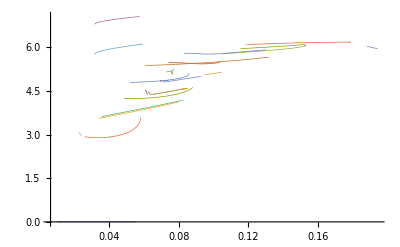

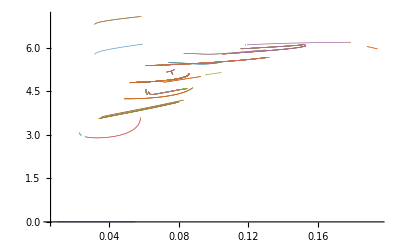

```mathematica
ListPlot[Table[branches[[i,All,{1,7}]],{i,Complement[Range[Length[branches]],DeleteDuplicates[Cases[distances,u_/;u[[3]]<1][[All,2]]]]}],Joined->True,PlotStyle->Directive[AbsoluteThickness[0.5]],PlotRange->All]
ListPlot[Table[branches[[i,All,{1,7}]],{i,Range[Length[branches]]}],Joined->True,PlotStyle->Directive[AbsoluteThickness[0.5]],PlotRange->All]
```

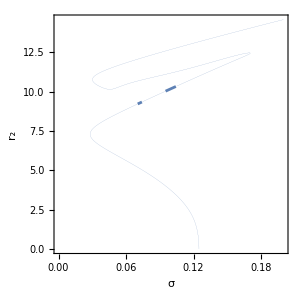
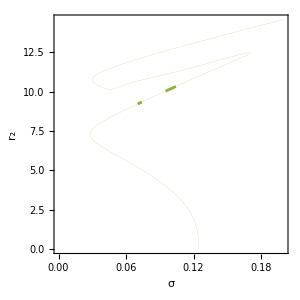
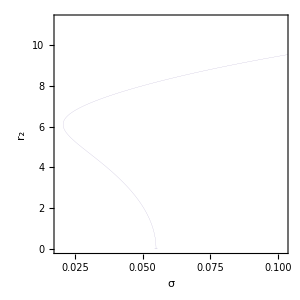
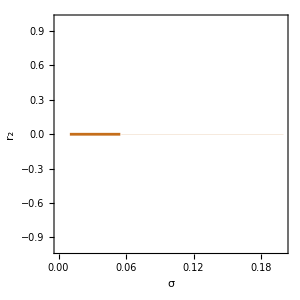
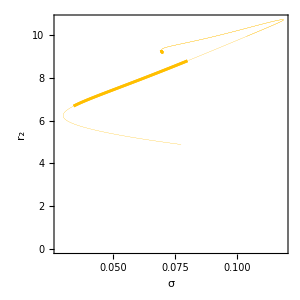
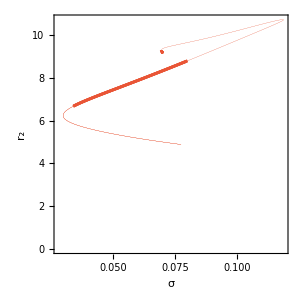
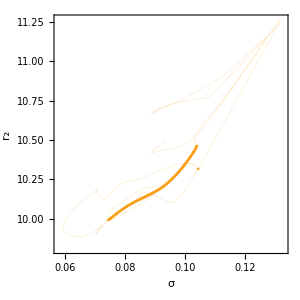
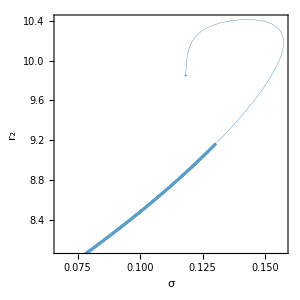

```mathematica
Table[Show[ListPlot[unstable[[i,All,All,{1,8}]],Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.1],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],ListPlot[stable[[i,All,All,{1,8}]],Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]]],{i,istable}]
```